```mathematica
messdaten vom runterfallen (Zeit zwischen den 2 marken)pro kugel eine spalte
```

```mathematica
data = {{2.15, 8.81, 6.09, 3.01, 3.62, 2.34, 1.59, 3.97}, {2.00, 8.91, 5.85, 3.89, 3.69, 2.37, 1.55, 3.92}, {2.00, 8.86, 5.96, 3.00, 3.65, 2.42, 1.65, 3.96}, {2.00, 8.93, 5.89, 3.06, 3.68, 2.47, 1.62, 3.96}, {2.04, 9.04, 6.09, 3.03, 3.56, 2.37, 1.54, 3.98}, {2.02, 8.96, 5.93, 3.02, 3.61, 2.43, 1.59, 3.80}, {2.01, 9.02, 5.96, 3.14, 3.56, 2.48, 1.65, 3.78}, {2.03, 9.01, 5.93, 3.06, 3.57, 2.31, 1.59, 3.78}, {1.97, 8.86, 5.81, 2.98, 3.53, 2.38, 1.56, 3.85}, {1.97, 8.87, 5.84, 3.11, 3.54, 2.31, 1.64, 3.83}};
mdata={Mean[data],StandardDeviation[data]}(*Mittelwert*)
```

{{2.019,8.927,5.935,3.13,3.601,2.388,1.598,3.883},{0.0513052,0.0786059,0.0961769,0.27158,0.0578216,0.0606996,0.0407704,0.0831398}}

```mathematica
r={{4.46, 1.96, 2.46, 3.46, 3.12, 3.96, 4.96, 2.96}}*10^-3/2(*Radien die dazugehören(gleiche spalte wie oben)*)
```

{{0.00223,0.00098,0.00123,0.00173,0.00156,0.00198,0.00248,0.00148}}

```mathematica
m={0.373,0.033,0.062,0.174,0.130,0.261,0.506,0.107} 10^-3(*masse der kugeln*)
```

{0.000373,0.000033,0.000062,0.000174,0.00013,0.000261,0.000506,0.000107}

```mathematica
R=50 10^-3(*innendurchmesser rohr*)
```

1/20

```mathematica
x = r/R//Flatten(*kugelradius durch Rohrradius*)
```

{0.0446,0.0196,0.0246,0.0346,0.0312,0.0396,0.0496,0.0296}

```mathematica
t1=Flatten[6 *Pi *r ];
t2=mdata[[1]]^-1*200 10^-3//Flatten;(*200 = fallstrecke = 20cm*)
t3=    m*9.81//Flatten;
t4=r^3*1262*9.81*4/3* Pi//Flatten;
t5=t3-t4;
t6=t1*t2;
y = t5/t6(*viskosität mit (m*g - r^3*g*ρ*V)/(6 π r ν))
```

{0.0420345,0.0184726,0.023185,0.0326097,0.0294053,0.0373221,0.0467469,0.0278973}

{0.0990589,0.0224039,0.0336984,0.0638978,0.0555401,0.0837521,0.125156,0.0515066}

{0.00365913,0.00032373,0.00060822,0.00170694,0.0012753,0.00256041,0.00496386,0.00104967}

{0.000575084,0.0000488085,0.0000965011,0.000268507,0.000196875,0.000402543,0.000790992,0.000168113}

{0.00308405,0.000274922,0.000511719,0.00143843,0.00107842,0.00215787,0.00417287,0.000881557}

{0.00416389,0.000413858,0.000781296,0.00208369,0.00163317,0.00312581,0.00585068,0.0014369}

{0.740664,0.664289,0.654962,0.69033,0.660324,0.690339,0.713228,0.613514}

```mathematica
dp=Table[{x[[i]],y[[i]]},{i,1,8}](*viskosität , r/R *)
```

{{0.0446,0.740664},{0.0196,0.664289},{0.0246,0.654962},{0.0346,0.69033},{0.0312,0.660324},{0.0396,0.690339},{0.0496,0.713228},{0.0296,0.613514}}

```mathematica
fit1=LinearModelFit[dp,t,t]
```

FittedModel[0.580429+2.86839 t]

```mathematica
fit1["ParameterTable"]
```

| Estimate | Standard Error | t Statistic | P-Value
1 | 0.580429 | 0.0376948 | 15.3981 | 4.74242×10^-6
t | 2.86839 | 1.06333 | 2.69756 | 0.0356918

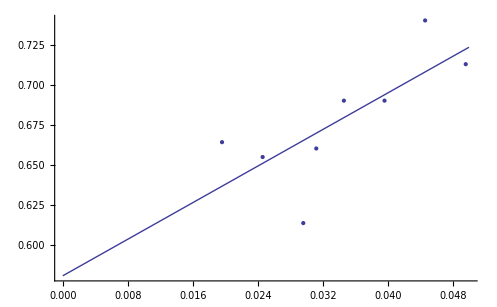

```mathematica
Show[ListPlot[dp],Plot[fit1[i],{i,0,0.05}]]
```

```mathematica
fit1[dp[[1,2]]](*nur a test*)
```

2.70494

```mathematica
op=Table[{dp[[i,2]]/fit1[dp[[i,1]]]},{i,1,8}]//Flatten(*η/steigung*)
```

{1.0456,1.04341,1.0061,1.01568,0.985672,0.9947,0.986892,0.922116}

```mathematica
Mean[op]
```

{1.00002}

```mathematica
StandardDeviation[op]
```

{0.039131}

```mathematica
Flatten[r]* 1262 * t2 * op^-1(*reynoldszahl*)
```

{0.266619,0.0265554,0.0519916,0.137352,0.110932,0.210391,0.396912,0.104327}

```mathematica
r(*radien*)
```

{{0.00223,0.00098,0.00123,0.00173,0.00156,0.00198,0.00248,0.00148}}